g2 square computation (level 3)
Dependencies: ModCatFunctions (NCAlgebra)

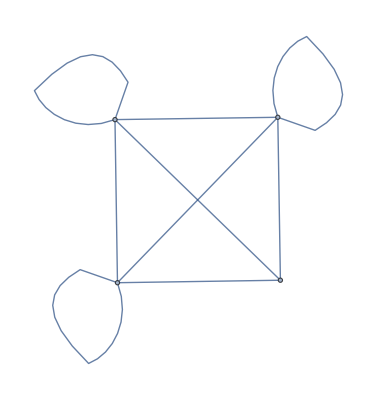

```mathematica
SetDirectory["~/Documents/UNH/Research/code/gen2/graph_18b"];
graph = { {0,1,1,1},{1,1,1,1},{1,1,1,1}, {1,1,1,1} };
AdjacencyGraph[ graph] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo];
BGamma = { {0,aa,bb,cc},{dd,ee,ff,gg},{hh,ii,jj,kk}, {ll,mm,nn,oo} };
q=Exp[2*Pi*I/42]; (* 2*Pi*I/(3*(4+ level)) *)
```

```mathematica
FullSimplify[q^10+q^8+q^2+1+q^-2+q^-8+q^-10]
```

1/2 (3+√21)

```mathematica
SetDirectory["~/Documents/UNH/Research/code/gen2/graph_18b/"]
lowOrderEqns = Import["lo.m"];
reducedLoEqs = Import["reducedLo.m"];
linearEqns = Import["linearEqns.m"];
linearSol = Import["linearSol.m"];
ItrEqs = Import["traceEqns.m"];
bigonEqns = Import["bigonEqns.m"];
trigonEqns = Import["trigonEqns.m"];
hiOrderEqns = Import["hi.m"];
reducedHiEqs = Import["reducedHi.m"];
squareEqns = Import["squareEqns.m"];
pentEqns = Import["pentEqns.m"];
```

/Users/calebhill/Documents/UNH/Research/code/gen2/graph_18b

```mathematica
loEqs = Import["reducedLo.m"];
reducedLoEqns = Import["reducedLo.m"];
hiEqs = Import["hi.m"];
linearEqs = Import["linearEqns.m"];
linearSol = Solve[linearEqs][[1]];
bigonEqns = Import["bigonEqns.m"];
trigonEqns = Import["trigonEqns.m"];
```

Hack:

```mathematica
loVariables=Union@Cases[loEqs,_Symbol,Infinity];
loVariables = DeleteCases[loVariables, True];
loVariables = DeleteCases[loVariables, Pi]
loVariables//Length
```

{alpha14,alpha15,alpha16,alpha25,alpha33,alpha34,alpha35,alpha40,alpha41,alpha45,alpha52,alpha53,alpha54}

13

```mathematica
hiVariables=Union@Cases[reducedHiEqs,_Symbol,Infinity];
hiVariables = DeleteCases[hiVariables, True];
hiVariables = DeleteCases[hiVariables, Pi]
hiVariables//Length
```

{alpha14,alpha15,alpha16,alpha25,alpha33,alpha34,alpha35,alpha40,alpha41,alpha45,alpha52,alpha53,alpha54}

13

Some relations deduced from the numerics:

```mathematica
relns = {alpha33->-alpha14, alpha52->alpha14,
alpha35->-alpha15, alpha53->alpha15,
alpha34->-alpha16, alpha54->alpha16,
alpha40->-alpha25, alpha41->-alpha25};
```

Get numeric expressions for all variables. From relations and numeric solution to reduced system

```mathematica
numerics = {alpha14->0.861006, alpha15->-1.694144, alpha16->-0.1556907, alpha25->1.391714, alpha33->-0.861006, alpha34->0.1556907, alpha35->1.694144, alpha40->-1.391714, alpha41->-1.391714, alpha45->-0.6193711, alpha52->0.861006, alpha53->-1.694144, alpha54->-0.1556907};
coefs = alpha/.linearSol/.numerics
```

{0.967919,1.39171,-1.39171,1.39171,-0.967919,-1.39171,-1.39171,-1.39171,0.967919,0.967919,1.39171,-1.39171,1.08393,0.861006,-1.69414,-0.155691,1.23799,-1.69414,0.155691,-0.619371,-1.23799,-0.155691,-0.619371,-1.69414,1.39171,-0.967919,-1.39171,1.23799,-1.69414,0.155691,-0.619371,-1.08393,-0.861006,0.155691,1.69414,-1.23799,-0.619371,1.69414,-0.155691,-1.39171,-1.39171,0.967919,-1.23799,-0.155691,-0.619371,-1.69414,-1.23799,-0.619371,1.69414,-0.155691,1.08393,0.861006,-1.69414,-0.155691}

```mathematica
(* a15+a16 *)
-1.694144-0.1556907
```

-1.84983

```mathematica
distincts = {};
indices = {};
tol = 0.0001;
For[ind1=1,ind1<=size,ind1++,
For[ind2=1,ind2<=size,ind2++,
For[ind3=1,ind3<=size,ind3++,
For[ind4=-expSize,ind4<= expSize,ind4++,
For[ind5=-expSize,ind5<= expSize,ind5++,
For[ind6=-expSize,ind6<= expSize,ind6++,

quant = NQIntsArr[[ind1,ind2,ind3,ind4+1+expSize,ind5+1+expSize,ind6+1+expSize]] ;
For[index=1,index<=dim2to1,index++,
If[Abs[coefs[[index]]-quant] < tol,
AppendTo[distincts, NQIntsArr[[ind1,ind2,ind3,ind4+1+expSize,ind5+1+expSize,ind6+1+expSize]]];
AppendTo[indices,{index, ind1,ind2,ind3,ind4+1+expSize,ind5+1+expSize,ind6+1+expSize}];
];]]
]]]]]
distincts = distincts//DeleteDuplicates;
```